```mathematica
(* doing some practical calculations with the lethargy concept *)

Clear["Global`*"];
source[x_]:=(1/(d*Sqrt[π]))*Exp[-(x-20)^2/d^2];


d=0.3;
a=10;
alp=(a-1)^2/(a+1)^2;
e0=20;
(* delay differential equation *)
eqn=D[Integrate[F[x]/((1-N[alp])*x),{x,e,e/N[alp]}]-F[e],e]==0
```

-(3.025 F[e])/e+(3.025 F[1.49383 e])/e-F'[e]==0

```mathematica
(* [alp*e0,e0] *)
```

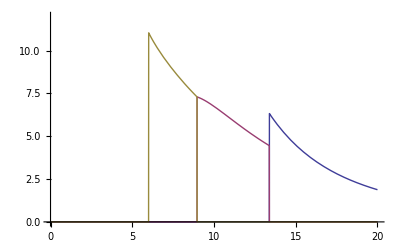

```mathematica
eqn1=D[Integrate[F1[x]/((1-N[alp])*x),{x,e,e0}]-F1[e],e]==0;
sol1=NDSolve[{eqn1,F1[20]==source[20]},F1,{e,N[alp]*e0,e0}];
g1[e_]:=If[(N[alp]*e0)≤e≤e0,F1[e]/.sol1[[1]][[1]],0.0001];

(* [alp^2*e0,alp*e0] *)
eqn2=D[Integrate[F2[x]/((1-N[alp])*x),{x,e,N[alp]*e0}]+Integrate[g1[x]/((1-N[alp])*x),{x,N[alp]*e0,e/N[alp]}]-F2[e],e]==0;
sol2=NDSolve[{eqn2,F2[N[alp]*e0]==Integrate[g1[x]/((1-N[alp])*x),{x,N[alp]*e0,e0}]},F2,{e,N[alp]^2*e0,N[alp]*e0}];
g2[e_]:=If[N[alp]^2*e0≤e≤N[alp]*e0,F2[e]/.sol2[[1]][[1]],0.0001];

(* [alp^3*e0,alp^2*e0] *)
eqn3=D[Integrate[F3[x]/((1-N[alp])*x),{x,e,N[alp]^2*e0}]+Integrate[g2[x]/((1-N[alp])*x),{x,N[alp]^2*e0,e/N[alp]}]-F3[e],e]==0;
sol3=NDSolve[{eqn3,F3[N[alp]^2*e0]==Integrate[g2[x]/((1-N[alp])*x),{x,N[alp]^2*e0,N[alp]^1*e0}]},F3,{e,N[alp]^3*e0,N[alp]^2*e0}];
g3[e_]:=If[N[alp]^3*e0≤e≤N[alp]^2*e0,F3[e]/.sol3[[1]][[1]],0.0001];

Plot[{g1[e],g2[e],g3[e]},{e,0.001,20},PlotRange->{0,12}]
```

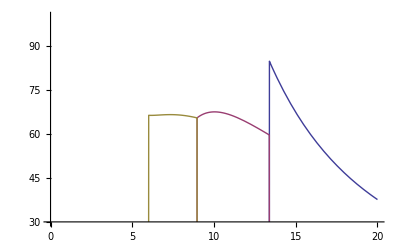

```mathematica
Plot[{g1[e]*e,g2[e]*e,g3[e]*e},{e,0.001,20},PlotRange->{{0,20},{30,100}}]
```